## Lab 6 - Gwen Gorman

The height (in meters) of a free-falling object is governed by the position function y[t]=-4.9 t^2+50t+6.1, provided zero is the height of the ground.

```mathematica
y[t_]:=-4.9 t^2+50t+6.1
```

What is the maximum height of the object?

```mathematica
y[tAtMaxY]
```

133.651

What is the time needed for the object to attain that height?

```mathematica
NSolve[y'[t]==0,t]
```

{{t→5.10204}}

```mathematica
tAtMaxY=(t/.%)[[1]]
```

5.10204

What is the speed, the velocity, and the acceleration of the object at the height of 100 meters going down?

```mathematica
NSolve[y[t]==100,t]
```

{{t→2.48144},{t→7.72264}}

```mathematica
tAt100=(t/.%)[[1]]
```

2.48144

```mathematica
Abs[y'[tAt100]] (* the speed *)
```

25.6819

```mathematica
y'[tAt100] (* the velocity *)
```

25.6819

```mathematica
y''[tAt100] (* the acceleration *)
```

-9.8

When does the object fall to the ground?

```mathematica
NSolve[y[t]==0]
```

{{t→-0.120575},{t→10.3247}}

```mathematica
tBackToGround=(t/.%)[[2]]
```

10.3247

Plot the position function together with the functions for the speed, the velocity, and the acceleration over the interval [0,T], where T is the result obtained in part 1.4.

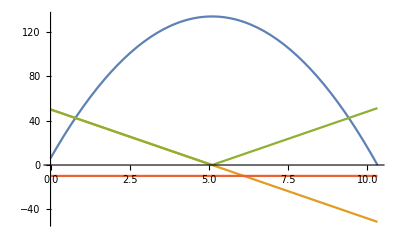

```mathematica
Plot[{y[t],y'[t],Abs[y'[t]],y''[t]},{t,0,tBackToGround},PlotRange->Automatic]
```

For x sin y-y sin x=2, use ContourPlot to draw its graph for -5≤x≤5,-5≤y≤5, and apply implicit differentiation to find the slope(s) of the level curve at x=1. Tips: When Solve and NSolve both fail to find the root of an equation, you may try FindRoot for the task.

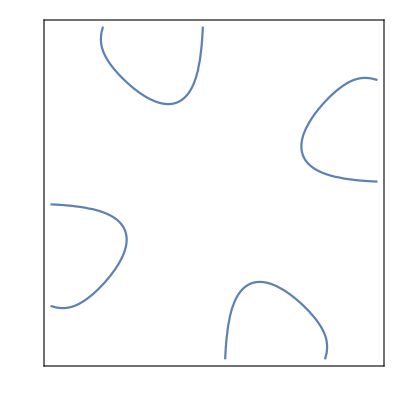

```mathematica
two[x_,y_] :=x Sin[y]-y Sin[x] ==2  
ContourPlot[Evaluate[two[x,y]], {x,-5,5},{y,-5,5}, FrameTicks->None]
```

```mathematica
twoy=FindRoot[Sin[y]-y Sin[1]==2,{y,100}]
```

{y→-2.78814}

```mathematica
y/. twoy
```

-2.78814

```mathematica
twoyprime= (y'[x]/.Solve[D[two[x,y[x]],x],y'[x]]/.{y[x]->y,y'[x]->y',x->1})
```

{(y Cos[1]-Sin[y])/(Cos[y]-Sin[1])}

```mathematica
twom=twoyprime/.twoy
```

{0.65198}

Refer to Question 2, plot the equation together with the tangent line at x=1. Tips: Use Show to combine graphs generated by ContourPlot and Plot into one single figure.

```mathematica
y0s=y/.twoy
```

-2.78814

A particle moves along the semicircle (x-3)^2+y^2=25,y≥0. Provided it moves in the x-direction at a constant rate x'(t)=0.5. Find the rate at which the particle is moving in the y-direction when x=2.

```mathematica
f[x]:=(x-3)^2+y^2==25;
D[f[x]/.{x-> x[t],f[x]->f[t]},t]
```

-9+30 t+6 t^2-12 t^3+5 t^4

```mathematica
dAdt/.{x->2,x'->.5}
```

-9+30 t+6 t^2-12 t^3+5 t^4

A 20-foot ladder leaning against a wall begins to slide. How fast is the top of the ladder sliding down the wall when the foot of the ladder is 8 feet to the wall and sliding away from the wall at the rate of 1 ft/sec?

```mathematica
eqn=x^2+y^2==20^2
D[eqn/.{x->x[t],y-> y[t]},t]
```

x^2+y^2==400

2 x[t] x'[t]+2 y[t] y'[t]==0

```mathematica
dAdt=(y'[t]/.Solve[%,y'[t]] /.{y[t]->y,x[t]->x,x'[t]->x'}//Simplify)[[1]]
```

-(x x')/y

```mathematica
dAdt/.{y->8,y'->1}
```

-(x x')/8

Find the linear approximation to f(x)=√x at x=4, and use it to approximate √3. Calculate the absolute error of the approximation to the exact value.

```mathematica
f[x_]:=√x
a=4;
P1[x_]:=f[a]+f'[a](x-a)//Simplify
P1[√3]
```

1/4 (4+√3)

```mathematica
N[1/4 (4+√3)]
```

1.43301

```mathematica
Abs[f[√3]-%]
```

0.116939

Find the quadratic approximation to f(x)=√x at x=4, and use it to approximate √3. Calculate the absolute error of the approximation to the exact value.

```mathematica
f[x_]:=√x
a=4;
P2[x_]:=f[a]+f'[a](x-a)+f''[a]/2(x-a)^2//Simplify
P2[√3]
```

3/64 (15+8 √3)

```mathematica
N[3/64 (15+8 √3)]
```

1.35264

```mathematica
Abs[f[√3]-%]
```

0.03657

Find the cubic approximation to f(x)=√x at x=4, and use it to approximate √3. Calculate the absolute error of the approximation to the exact value.

```mathematica
f[x_]:=√x
a=4;
P3[x_]:=f[a]+f'[a](x-a)+f''[a]/2(x-a)^2+f'''[a]/6(x-a)^3//Simplify
P3[√3]
```

1/512 (260+243 √3)

```mathematica
N[1/512 (260+243 √3)]
```

1.32986

```mathematica
Abs[f[√3]-%]
```

0.013786

Refer to Questions 6-8. Plot √x together with its linear, quadratic, and cubic approximations at x=4, for 0≤x≤6. Compare the three absolute errors, when used to approximate √3, and explain the difference.

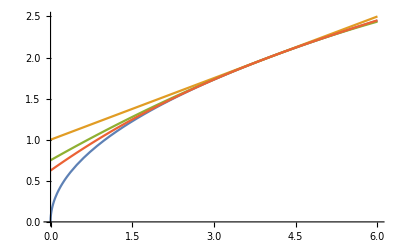

```mathematica
Plot[{f[x],P1[x],P2[x],P3[x]},{x,0,6}]
```

Based on the graph, you can see that the three absolute errors are all relatively similar when used to approximate √3. However they  all have different y values when x is 0. Looking at the graph, the linear approximation has the largest absolute error, then the quadratic approximation, and lastly the cubic approximation has the smallest absolute error when trying the approximate the value of √3.

Use a differential to estimate sin 50°. Note: By default, all Mathematica trigonometric functions take argument in radians. But you may call a function like Sin[50 Degree].

```mathematica
f[x_]:= Sin[50Degree]
dx=Sin[49Degree]-Sin[50Degree];
df=f'[x]dx/.x->Sin[50Degree]
```

0

```mathematica
f[Sin[50Degree]]+df//N
```

0.766044

Use Newton’s method to find all real roots of f(x)=x^5-3 x^4+2 x^3+15 x^2-9x.

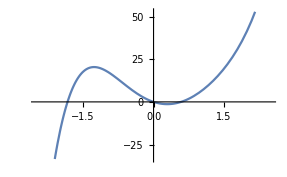

```mathematica
f[x_]:=x^5-3 x^4+2 x^3+15 x^2-9x
Plot[f[x],{x,-2.5,2.5}]
```

```mathematica
newton[x_]:=x-f[x]/f'[x]
NestList[newton,-1.9,10]
```

{-1.9,-1.83867,-1.83326,-1.83322,-1.83322,-1.83322,-1.83322,-1.83322,-1.83322,-1.83322,-1.83322}

```mathematica
f[-1.83322]==0
```

False

```mathematica
NestList[newton,0,10]
```

{0,0,0,0,0,0,0,0,0,0,0}

```mathematica
f[0]==0
```

True

```mathematica
NestList[newton,.6,10]
```

{0.6,0.586875,0.586596,0.586596,0.586596,0.586596,0.586596,0.586596,0.586596,0.586596,0.586596}

```mathematica
f[0.586596]==0
```

False